# Modeling Groundwater Flow Around Wells with Discharge Potential : Analytical Approaches for 1D Confined/Unconfined Aquifers and 2D Flow.

```mathematica
ClearAll["Global`*"]
```

The discharge potential, Φ, is a scalar function that simplifies the governing equations of groundwater flow by satisfying Laplace' s equation, enabling the use of potential flow theory and the principle of superposition .

Darcy’s Law (for homogeneous, isotropic media) is given as:

						q_x = - k (∂h)/(∂x) ,     q_y = - k (∂h)/(∂y),     q_z = - k (∂h)/(∂z)

The continuity equation for steady-state flow in a homogeneous and isotropic medium is: (assuming Dupuit-Forchheimer approximation, ignoring vertical flow):
								     (∂q_x)/(∂x) + (∂q_y)/(∂y) = 0 

Combining with Darcy’s Law yields Laplace’s equation for head:
											(∂^2 h)/(∂x^2) + (∂^2 h)/(∂y^2) = 0 				

Discharge Potential
The discharge potential Φ(x,y) is introduced to simplify the governing equations. For a confined aquifer, the discharge potential is defined as: Φ = K b h. So the discharge vector components in this case are given as:

								             	      Q_x = -(∂Φ)/(∂x) ,     Q_y = -(∂Φ)/(∂y)

Substituting these into the continuity equation yields Laplace’s equation for the discharge potential:

												(∂^2 Φ)/(∂x^2) + (∂^2 Φ)/(∂y^2)
													
The discharge potential for an unconfined aquifer is defined as:   Φ = 1/2 K h^2

### 1 D Groundwater Flow Using Discharge Potential (Φ) - Combined confined and unconfined flow.

```mathematica
(*Parameters Definition*)
L=500;     (*Aquifer length (m)*)
b=20;       (*Aquifer thickness (m)*)
K=0.001;(*Hydraulic conductivity (m/s)*)
h0=30;    (*Head at x=0 (m)*)
hL=5;      (*Head at x=L (m)*)
```

#### Solve for the Discharge Potential

```mathematica
(*Discharge potential definitions*)
PhiConfined[h_]:=K b h-0.5 K b^2; (*Confined region*)
PhiUnconfined[h_]:=0.5 K h^2;        (*Unconfined region*)
PhiInterface=0.5 K b^2;                      (*Discharge potential at the interface*)

(*Boundary conditions for Phi*)(*Phi is the discharge potential*)
Phi0=PhiConfined[h0];                   (*Phi at x=0*)
PhiL=PhiUnconfined[hL];               (*Phi at x=L*)

(*Linear potential solution for Phi(x)*) (*Interface potential (where h=b)*)
Phi[x_]:=(PhiL-Phi0)/L x +Phi0;

(*Find the interface location where h(x)=b*)
xInterface=x/. Solve[Phi[x]==PhiInterface,x][[1]];
```

#### Compute the Head Distribution

```mathematica
h[x_]:=If[x≤xInterface,
(Phi[x]+0.5 K b^2)/(K b),(*Confined solution*)
√((2 Phi[x])/K)                  (*Unconfined solution*)
];
```

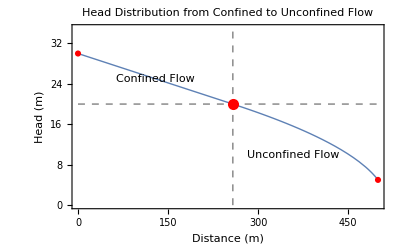

```mathematica
Show[
Plot[h[x],{x,0,L},
PlotStyle->Thick,
PlotRange->{{0,L},{0,35}},
Frame->True,
FrameLabel->{"Distance (m)","Head (m)"},
PlotLabel->Style["Head Distribution from Confined to Unconfined Flow",12,Bold],
Epilog->{
(*Grid line at xInterface*)
{Dashed,Gray,Line[{{xInterface,0},{xInterface,35}}]},
(*Grid line at head b*)
{Dashed,Gray,Line[{{0,b},{L,b}}]},

(*Labels and point*)
Text["Confined Flow",{xInterface/2,25}],
Text["Unconfined Flow",{xInterface+100,10}],
Red,PointSize[0.02],Point[{xInterface,b}]
}
],
ListPlot[{{0,h0},{L,hL}},PlotStyle->Red,PlotMarkers->Automatic,Frame->True]
]
```

### 2 D Groundwater Flow Around Pumping Wells

Radial Flow rate:
						Q_r = Q/(2 π r) = -(d Φ)/(d r)

Integrating with boundary condition Φ(r_0)= Φ_0 :

						Φ(r) = Q/(2 π) ln (r/r_0) + Φ_0

To form flownet,streamlines should be drawn which aslo satisfies the laplace's equation. Streamlines are tangential to flow vectors
and intersect the equipotentials perpendicularly. The stream function is 
							ψ = Q/(2 π) tan^-1(y/x) (in Cartesian coordinate)

#### Single Well Solution

Discharge Potential for a well in polar coordinates:
Φ(r) = Q/(2 Π)ln(r) + C 
Q is the pumping rate, r is the radial distance from the well,and C is a constant determined by the boundary conditions.

```mathematica
Q1=15;                       (*Pumping rate (m.b3/s)*)
well = {100,250}; (*Pumping well location*)
r0=10;     (*Reference distance (m) (if not using obWell)*)
Phi0=32;(*Reference potential*)
K=0.01;(*Hydraulic conductivity (m/s)*)

(*Distance and angle from well to any (x,y)*)
rr[x_,y_]:=√((x-well[[1]])^2+(y-well[[2]])^2);
thetaa[x_,y_] = ArcTan[x-well[[1]],y-well[[2]]];

(*Discharge potential and stream function*)
PhiWell[x_,y_]:=(Q1/(2 Pi))*Log[rr[x,y]/r0]+Phi0;
PsiWell[x_,y_]:=(Q1/(2 Pi))*thetaa[x,y];
HeadOneWell[x_,y_]:=√((2 PhiWell[x,y])/K);
```

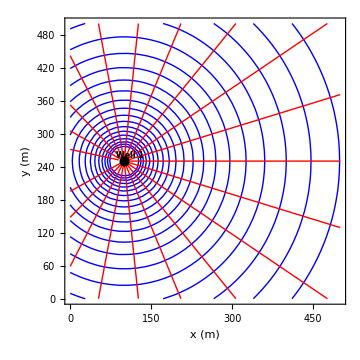
-Graphics-Flow Net for Single Pumping Well

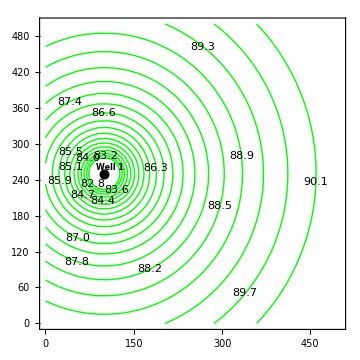
-Graphics-Hydraulic Head around a Single Pumping Well

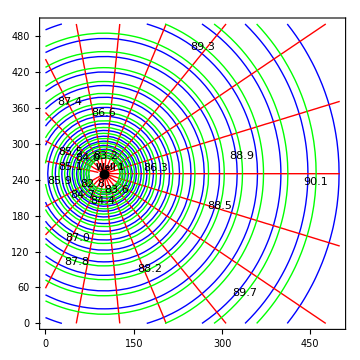

```mathematica
(*Plotting function for flow net*)
PlotFlowNet[phi_,psi_,range_,title_]:=Module[{},
Labeled[
Show[
ContourPlot[phi[x,y],{x,range[[1]],range[[2]]},{y,range[[3]],range[[4]]},
Contours->20,ContourShading->None,ContourStyle->Blue],
ContourPlot[psi[x,y],{x,range[[1]],range[[2]]},{y,range[[3]],range[[4]]},
Contours->20,ContourShading->None,ContourStyle->Red],
Graphics[{
Black,PointSize[0.02],Point[well],
Text[Style["Well 1",8,Bold],well+{10,10}]
}],
ImageSize->Medium,
Axes->True,
Frame->True,
FrameLabel->{"x (m)","y (m)"}],
Style[title,12,Bold],Top]
]

(*Single well flow net*)
PlotFlowNet[PhiWell,PsiWell,{0,500,0,500},"Flow Net for Single Pumping Well"]

(*####################################################################################*)
(*To show the head*)
PlotHeadOneWell[head_,range_,title_]:=Module[{},
Labeled[
Show[
ContourPlot[head[x,y],{x,range[[1]],range[[2]]},{y,range[[3]],range[[4]]},
Contours->20,ContourShading->None,ContourStyle->Green,
ContourLabels->Function[{x,y,z},Text[NumberForm[z,{4,1}],{x,y},Background->White]]],
Graphics[{
Black,PointSize[0.02],Point[well],
Text[Style["Well 1",8,Bold],well+{10,10}]
}],
ImageSize->Medium,
Axes->True,
Frame->True],
Style[title,12,Bold],Top]
]

PlotHeadOneWell[HeadOneWell,{0,500,0,500},"Hydraulic Head around a Single Pumping Well"]

(*####################################################################################*)

PlotFlowNet[phi_,psi_,head_,range_,title_]:=Module[{},
Labeled[
Show[
ContourPlot[phi[x,y],{x,range[[1]],range[[2]]},{y,range[[3]],range[[4]]},
Contours->20,ContourShading->None,ContourStyle->Blue],
ContourPlot[psi[x,y],{x,range[[1]],range[[2]]},{y,range[[3]],range[[4]]},
Contours->20,ContourShading->None,ContourStyle->Red],
ContourPlot[head[x,y],{x,range[[1]],range[[2]]},{y,range[[3]],range[[4]]},
Contours->20,ContourShading->None,ContourStyle->Green,
ContourLabels->Function[{x,y,z},Text[NumberForm[z,{4,1}],{x,y},Background->White]]],
Graphics[{
Black,PointSize[0.02],Point[well],
Text[Style["Well 1",8,Bold],well+{10,10}]
}],
ImageSize->Medium,
Axes->True,
Frame->True],
Style[title,12,Bold],Top]
]

(*Single well flow net*)
PlotFlowNet[PhiWell,PsiWell,HeadOneWell,{0,500,0,500}," "]
```

#### Multiple Well Solution

```mathematica
(*Two wells parameters*)
Q1=30;(*m.b3/s*)
Q2=35;(*m.b3/s*)
well1={150,300}; (*location of the first well*)
well2={350,100}; (*location of the second well*)
obsWell={400,300}; (*An observation well*)
h0=80;    (*Observed head (m)*)
K=0.01;(*Hydraulic conductivity (m/s)*)

(*Distance functions*)
r1[x_,y_]:=√((x-well1[[1]])^2+(y-well1[[2]])^2);
r2[x_,y_]:=√((x-well2[[1]])^2+(y-well2[[2]])^2);
rObs=r1[obsWell[[1]],obsWell[[2]]];

(*Reference potential at the observed well*)
Phi0=0.5 K h0^2;

(*Superposed potential and stream function*)
PhiTwoWells[x_,y_]:=
(Q1/(2 Pi))*Log[r1[x,y]/rObs]+(Q2/(2 Pi))*Log[r2[x,y]/rObs]+Phi0;

PsiTwoWells[x_,y_]:=
(Q1/(2 Pi))*ArcTan[x-well1[[1]],y-well1[[2]]]+
(Q2/(2 Pi))*ArcTan[x-well2[[1]],y-well2[[2]]];
```

#### Uniform Flow with Wells

```mathematica
(*Uniform flow parameters*)
Quniform=0.04;(*m.b2/s*)

(*Combined potential and stream function*)
PhiUniform[x_,y_]:=-Quniform*x+PhiTwoWells[x,y];
PsiUniform[x_,y_]:=-Quniform*y+PsiTwoWells[x,y];
```

#### Flow Net Visualization

```mathematica
plotFlowNet[phi_,psi_,range_,title_]:=Module[{},
Labeled[
Show[
(*Plot for phi -  discharge potential*)
ContourPlot[phi[x,y],{x,range[[1]],range[[2]]},{y,range[[3]],range[[4]]},
Contours->20,ContourShading->None,ContourStyle->Blue(*, ContourLabels->Function[{x,y,z},Text[NumberForm[z,{4,1}],{x,y},Background->White]]*)],
(*Plot for psi -  stream potential*)
ContourPlot[psi[x,y],{x,range[[1]],range[[2]]},{y,range[[3]],range[[4]]},
Contours->20,ContourShading->None,ContourStyle->Red(*, ContourLabels->Function[{x,y,z},Text[NumberForm[z,{4,1}],{x,y},Background->White]]*)],
Graphics[{
Black,PointSize[0.02],Point[well1],Point[well2],
Text[Style["Well 1",8,Bold],well1+{10,10}],
Text[Style["Well 2",8,Bold],well2+{10,10}]
}],
ImageSize->Medium,
Axes->True,
Frame->True],
Style[title,12,Bold],Top]
]
```

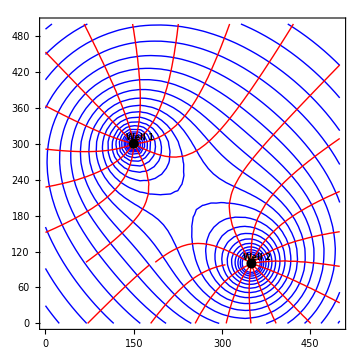
-Graphics-Two Wells -  Contour plot of equipotentails and streamlines

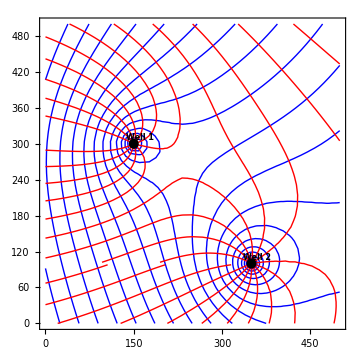
-Graphics-Wells in Uniform Flow

```mathematica
(*Two wells flow net*)
plotFlowNet[PhiTwoWells,PsiTwoWells,{0,500,0,500},"Two Wells -  Contour plot of equipotentails and streamlines"]

(*Wells in uniform flow*)
plotFlowNet[PhiUniform,PsiUniform,{0,500,0,500},"Wells in Uniform Flow"]
```

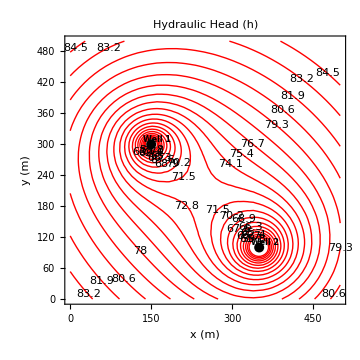

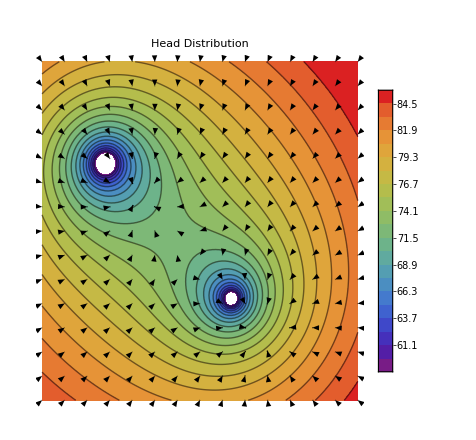

```mathematica
(*Convert potential to head*)
HeadTwoWells[x_,y_]:=√((2 PhiTwoWells[x,y])/K);

(*Enhanced contour plotting with values*)
PlotHead[func_,range_,title_,ncontours_]:=
ContourPlot[
func[x,y],{x,range[[1]],range[[2]]},{y,range[[3]],range[[4]]},
Contours->ncontours,ContourStyle->Red,ContourShading->None,PlotLabel->Style[title,12,Bold],FrameLabel->{"x (m)","y (m)"},ContourLabels->Function[{x,y,z},Text[NumberForm[z,{4,1}],{x,y},Background->White]],
Epilog->{
Black,PointSize[0.02],Point[well1],Point[well2],
Text[Style["Well 1",8,Bold],well1+{10,10}],
Text[Style["Well 2",8,Bold],well2+{10,10}]},
PlotRangePadding->Scaled[0.05],ImageSize->Medium 
]

PlotHead[HeadTwoWells,{0,500,0,500},"Hydraulic Head (h)",20]

Needs["VectorFieldPlots`"];

(*Head Values*)
headValues=Table[HeadTwoWells[x,y],{x,0,500,5},{y,0,500,5}];

(*Contour plot of head*)
headcontourplot = 
ListContourPlot[
headValues,DataRange->{{0,500},{0,500}},
PlotLegends->Automatic,FrameLabel->{"x (m)","y (m)"},
PlotLabel->Style["Head Distribution",12,Bold],ColorFunction->"Rainbow",Contours->20,ContourLabels->Automatic
];

(*Interpolate headValues for gradient calculation*)
hInterpolated=ListInterpolation[headValues,{{0,500},{0,500}}];

(*Gradient plot*)
vectorplot=GradientFieldPlot[-hInterpolated[x,y],{x,0,500},{y,0,500},PlotPoints->15,ScaleFactor->3];

(*Overlay with contour plot*)
Show[headcontourplot,vectorplot,Frame-> False,AspectRatio->22/20.]
```

# Modelling Steady Groundwater Flow around pumping wells in an Heterogeneous and Anisotropic unconfined aquifer using discharge potential .

```mathematica
ClearAll["Global`*"]
```

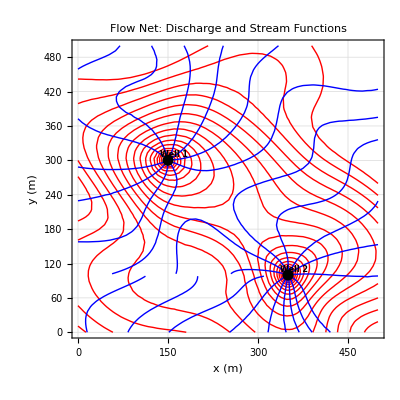

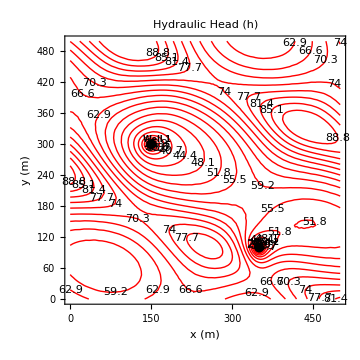

-Graphics-

```mathematica
(*Two wells parameters*)
Q1=30; (*m.b3/s*)
Q2=35; (*m.b3/s*)
well1={150,300}; (*location of the first well*)
well2={350,100}; (*location of the second well*)
obsWell={400,300}; (*An observation well*)
h0=80; (*Observed head (m)*)

(*Anisotropic hydraulic conductivities (Kx≠Ky)*)
(*KxFunc[x_,y_]:=0.01; (*Spatially varying Kx*)
KyFunc[x_,y_]:=0.005; (*Spatially varying Ky*)
*)
(*Heterogeneity:function for spatially varying K*)
KxFunc[x_,y_]:=0.01+0.005 Sin[0.01 x+0.02 y];
KyFunc[x_,y_]:=0.01+0.003 Cos[0.015 x-0.01 y];

(*Effective conductivity for potential*)
Keff[x_,y_]:=√(KxFunc[x,y]* KyFunc[x,y]);

(*Transformed distances for anisotropy*)
r1Aniso[x_,y_]:=√((x-well1[[1]])^2/KxFunc[x,y] + (y-well1[[2]])^2/KyFunc[x,y]);

r2Aniso[x_,y_]:= √((x-well2[[1]])^2/KxFunc[x,y] + (y-well2[[2]])^2/KyFunc[x,y]);

r1ObsAniso=r1Aniso@@obsWell;
r2ObsAniso=r2Aniso@@obsWell;

(*Reference potential at the observed well*)
Phi0=0.5*Keff@@obsWell*h0^2;

(*Superposed potential and stream function*)
PhiTwoWells[x_,y_]:=
(Q1/(2 Pi) Log[r1Aniso[x,y]/r1ObsAniso]) + (Q2/(2 Pi) Log[r2Aniso[x,y]/r2ObsAniso]) +Phi0;

(*Stream function approximation for anisotropy*)
PsiTwoWells[x_,y_]:=
Q1/(2 Pi) ArcTan[(x-well1[[1]]) √(KyFunc[x,y]/KxFunc[x,y]) , (y-well1[[2]]) √(KxFunc[x,y]/KyFunc[x,y])]   + Q2/(2 Pi) ArcTan[(x-well2[[1]]) √(KyFunc[x,y]/KxFunc[x,y]) , (y-well2[[2]]) √(KxFunc[x,y]/KyFunc[x,y])];

(*Visualization*)
Show[
ContourPlot[
PhiTwoWells[x,y],{x,0,500},{y,0,500},
Contours->20,ContourShading->None,ContourStyle->Red
(*,ContourLabels->Function[{x,y,z},Text[NumberForm[z,{4,1}],{x,y},Background->White]]*)],ContourPlot[
PsiTwoWells[x,y],{x,0,500},{y,0,500},
Contours->20,ContourShading->None,ContourStyle->Blue
(*,ContourLabels->Function[{x,y,z},Text[NumberForm[z,{4,1}],{x,y},Background->White]]*)],Graphics[{
Black,PointSize[0.02],Point[well1],Point[well2],Text[Style["Well 1",8,Bold],well1+{10,10}],Text[Style["Well 2",8,Bold],well2+{10,10}]}
],
Frame->True,Axes->True,FrameLabel->{"x (m)","y (m)"},GridLines->Automatic,PlotLabel->Style["Flow Net: Discharge and Stream Functions",12,Bold]]

(*#######################################################*)

(*Convert potential to head*)
HeadTwoWells[x_,y_]:=√((2 PhiTwoWells[x,y])/Keff[x,y]);

(*Enhanced contour plotting with values*)
PlotHead[func_,range_,title_,ncontours_]:=
ContourPlot[
func[x,y],{x,range[[1]],range[[2]]},{y,range[[3]],range[[4]]},
Contours->ncontours,ContourStyle->Red,ContourShading->None,PlotLabel->Style[title,12,Bold],FrameLabel->{"x (m)","y (m)"},ContourLabels->Function[{x,y,z},Text[NumberForm[z,{4,1}],{x,y},Background->White]],
Epilog->{
Black,PointSize[0.02],Point[well1],Point[well2],
Text[Style["Well 1",8,Bold],well1+{10,10}],
Text[Style["Well 2",8,Bold],well2+{10,10}]},
PlotRangePadding->Scaled[0.05],ImageSize->Medium 
]

PlotHead[HeadTwoWells,{0,500,0,500},"Hydraulic Head (h)",20]

Needs["VectorFieldPlots`"];

(*Head Values*)
headValues=Table[HeadTwoWells[x,y],{x,0,500,1},{y,0,500,1}];

(*Contour plot of head*)
headcontourplot = 
ListContourPlot[
headValues,DataRange->{{0,500},{0,500}},
PlotLegends->Automatic,FrameLabel->{"x (m)","y (m)"},
PlotLabel->"Head Distribution",ColorFunction->"Rainbow",Contours->20,ContourLabels->Automatic];

(*Interpolate headValues for gradient calculation*)
hInterpolated=ListInterpolation[headValues,{{0,500},{0,500}}];

(*Gradient plot*)
vectorplot=GradientFieldPlot[-hInterpolated[x,y],{x,0,500},{y,0,500},PlotPoints->15,ScaleFactor->3];

(*Overlay with contour plot*)
Show[headcontourplot,vectorplot,Frame-> False,AspectRatio->22/20.]
```

#### Interactive Parameter Exploration For real-time adjustment of well pumping rates and other paramaters.

```mathematica
Manipulate[
(*Define well positions dynamically*)
well1={x1,y1};
well2={x2,y2};

(*Reference distances from a fixed observation point*)
obsWell={400,300};

(*Heterogeneity:function for spatially varying K*)
KxFunc[x_,y_]:=0.01+0.005 Sin[0.01 x+0.02 y];
KyFunc[x_,y_]:=0.01+0.003 Cos[0.015 x-0.01 y];

r1Aniso[x_,y_]:=√((x-well1[[1]])^2/KxFunc[x,y] + (y-well1[[2]])^2/KyFunc[x,y]);

r2Aniso[x_,y_]:=√((x-well2[[1]])^2/KxFunc[x,y] + (y-well2[[2]])^2/KyFunc[x,y]);

r1ObsAniso=r1Aniso@@obsWell;
r2ObsAniso=r2Aniso@@obsWell;

Keff[x_,y_]:=√(KxFunc[x,y]* KyFunc[x,y]);

(*Discharge potential at observation well*)
Phi0=0.5 Keff@@obsWell h0^2;

(*Discharge potential function*)
PhiInteractive[x_,y_]:=
Q1/(2 Pi) Log[r1Aniso[x,y]/r1ObsAniso]+Q2/(2 Pi) Log[r2Aniso[x,y]/r2ObsAniso]+Phi0;

(*Stream function (approximate elliptical coordinates)*)
PsiInteractive[x_,y_]:=
Q1/(2 Pi) ArcTan[(x-well1[[1]]) √(KyFunc[x,y]/KxFunc[x,y]),(y-well1[[2]]) √(KxFunc[x,y]/KyFunc[x,y])]+Q2/(2 Pi) ArcTan[(x-well2[[1]]) √(KyFunc[x,y]/KxFunc[x,y]),(y-well2[[2]]) √(KxFunc[x,y]/KyFunc[x,y])];

(*Plot equipotential lines*)
ContourPlot[
PhiInteractive[x,y],{x,0,500},{y,0,500},
Contours->20,ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotLabel->"Interactive Two-Well Equipotential Plot",FrameLabel->{"x (m)","y (m)"},ContourLabels->Function[{x,y,z},Text[NumberForm[z,{4,1}],{x,y},Background->White]],
Epilog->
{Black,PointSize[Large],Point[{x1,y1}],Point[{x2,y2}],
Text[Style["Well 1",8,Bold],{x1,y1}+{10,10}],
Text[Style["Well 2",8,Bold],{x2,y2}+{10,10}]}
],

(*Controls*)
{{Q1,30},10,50},{{Q2,35},10,50},
{{x1,150},0,500},{{y1,300},0,500},
{{x2,350},0,500},{{y2,100},0,500},
{{h0,80},10,100}  (*Head at the observation well*)]
```

# Discharge Potential for a Transient (Unsteady) Flow around Pumping Wells with Theis Equation.

```mathematica
ClearAll["Global`*"]
```

#### The Theis solution describes transient radial flow to a well in a confined aquifer. The drawdown s(r,t) = h0 - h(r,t) s(r,t) = Q/(4 π T) W(u); u = (r^2 S)/(4 T t) W(u) = - γ - ln(u) + ∑_(k=1)^∞ ((-1)^(k+1)u^k)/(k * k!) (*where γ is the Euler–Mascheroni constant*)

```mathematica
(*Aquifer parameters*)
K=0.01;    (*Hydraulic conductivity[m/s]*)
S=0.001;  (*Storativity[dimensionless]*)
b= 20;       (*assuming aquifer thickness*)
T=K*b;    (*Transmissivity[m.b2/s]*)
Q1=30;    (*Discharge (pumping) rate[m.b3/s]*)
Q2= 35;
h0 = 80;  (*assuming initial head*)

(*Well locations*)
well1={150,300};
well2={350,100};

(*Well function*)
W[u_,n_Integer?Positive]:= -N[EulerGamma,100]-Log[u]+Sum[(-1)^(k+1) u^k/(k Factorial[k]),{k,1,n}];

(*Drawdown due to Theis equation*)
drawdown[{x_,y_},t_]:=
Module[{r1,r2,u1,u2,s1,s2},
r1=√((x-well1[[1]])^2+(y-well1[[2]])^2);
r2=√((x-well2[[1]])^2+(y-well2[[2]])^2);
u1=(r1^2 S)/(4 T t);
u2=(r2^2 S)/(4 T t);
s1=(Q1/(4 Pi T)) W[u1,100];
s2=(Q2/(4 Pi T)) W[u2,100];
s1+s2
]

t=3600;

(*Calculating head due to both wells*)
HeadTotal[x_,y_,t_]:=h0-drawdown[{x,y},t];

(*3D surface plot of head at t = 3600*)
Plot3D[
HeadTotal[x,y,t],{x,0,500},{y,0,500},
AxesLabel->{"x (m)","y (m)","Head (m)"},
PlotLabel->Style["2-Well Theis Head Surface at t = 1 hr",12,Bold],
ImageSize->Medium,PlotPoints->70,ColorFunction->"Rainbow",Boxed->True,PlotLegends->Automatic
]
```

-Graphics3D-

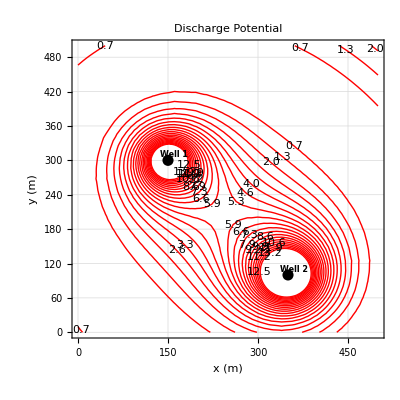

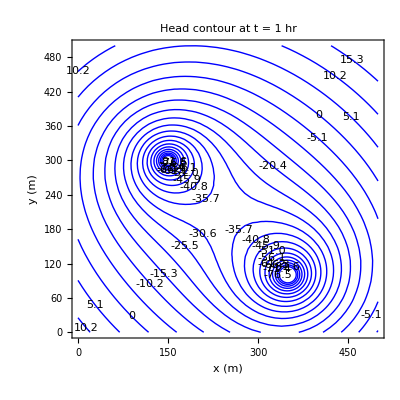

-Graphics-

```mathematica
(*Discharge potential of the transient flow in an unconfined aquifer*)
PhiTransientFlow[x_,y_]:= 0.5 * K * HeadTotal[x,y,t]^2;

(*Visualization*)
Show[
ContourPlot[
PhiTransientFlow[x,y],{x,0,500},{y,0,500},
Contours->20,ContourShading->None,ContourStyle->Red
,ContourLabels->Function[{x,y,z},Text[NumberForm[z,{4,1}],{x,y},Background->White]]],
Graphics[{
Black,PointSize[0.02],Point[well1],Point[well2],
Text[Style["Well 1",8,Bold],well1+{10,10}],
Text[Style["Well 2",8,Bold],well2+{10,10}]}
],
Frame->True,Axes->True,FrameLabel->{"x (m)","y (m)"},GridLines->Automatic,PlotLabel->Style["Discharge Potential",12,Bold]]

ContourPlot[
HeadTotal[x,y,t],{x,0,500},{y,0,500},
ContourShading->None,Contours->20,ContourStyle->Blue,FrameLabel->{"x (m)","y (m)"},PlotLabel->Style["Head contour at t = 1 hr",12,Bold],ContourLabels->Function[{x,y,z},Text[NumberForm[z,{4,1}],{x,y},Background->White]]
]

Needs["VectorFieldPlots`"];

(*Head Values*)
headValues=Table[HeadTotal[x,y,t],{x,0,500,1},{y,0,500,1}];

(*Contour plot of head*)
headcontourplot = 
ListContourPlot[
headValues,DataRange->{{0,500},{0,500}},
PlotLegends->Automatic,FrameLabel->{"x (m)","y (m)"},
PlotLabel->Style["Head Distribution at t = 1 hr",12,Bold],ColorFunction->"Rainbow",Contours->20,ContourLabels->Automatic];

(*Interpolate headValues for gradient calculation*)
hInterpolated=ListInterpolation[headValues,{{0,500},{0,500}}];

(*Gradient plot*)
vectorplot=GradientFieldPlot[-hInterpolated[x,y],{x,0,500},{y,0,500},PlotPoints->15,ScaleFactor->3];

(*Overlay with contour plot*)
Show[headcontourplot,vectorplot,Frame-> False]
```

# Final Remarks and Conclusion This project and codes addressed the problem of modeling groundwater flow around pumping wells in an aquifers (confined and unconfined ) using discharge potential theory, building on the analytical framework presented by Korkmaz (2017). The study focused on solving steady-state flow problems in confined, unconfined, and combined aquifer systems, leveraging the linearity of Laplace’s equation to apply superposition principles for multi-well and uniform flow scenarios. I extend and solve the analytical solutions presented in Korkmaz (2017) to anisotropic and heterogeneous aquifers via coordinate transformation. I finally use the classical Theis’ equation for transient (time-dependent) groundwater flow to compute the head and the discharge potential around 2 pumping wells in an unconfined aquifer system. The code start with solving the 1D groundwater flow using discharge potential combining the unconfined and unconfined flow, then to radial flow around a single well. After establishing the discharge potential and stream function for a single well , I solve the analytical solution around 2 wells using the superposition principle (due to linearity of Laplace’s equation) for homogenous isotropic aquifer system and heterogenous anisotropic aquifer system. The final part of the code is for the transient flow.

# References 1. Korkmaz, S. (2017). Analytical solutions to groundwater flow around Wells using discharge potential. In Proceedings of the 10th World Congress of EWRA ‘Panta Rei’, Athens, Greece (pp. 5-9). 2. Theis, C. V. (1935). The relation between the lowering of the piezometric surface and the rate and duration of discharge of a well using ground-water storage. Transactions American Geophysical Union, 16(2), 519-524. https://doi.org/10.1029/TR016i002p00519